# Studying the evolution of density distribution in a discrete graph

Ananya Mukherjee

University of Massachusetts, Lowell

Abstract: In this project we are studying the clustering of mass on a discrete graph model under the influence of gravity. This simple model could be used as a first step to study the formation of the Large Scale structure in the Universe, with the underlying manifold being described by discrete hypergraph.

## Introduction

At an enormous scale (~ 100Mpc), bigger than the length scale of individual galaxies the Universe displays a web-like structure, with galaxies bounded gravitationally forming a filament like structure of galaxy clusters,  punctured by empty spaces (void) with very few galaxies inside. All these massive structures in the Universe  is known as the Large Scale structure (LSS) of the spacetime. The gravitational interaction between them is the key factor that determines the evolution of the Universe. Over the course of time the galaxies are drifting toward each other forming a cluster and supercluster subsequently. It is believed that the Milky way is merging toward the Virgo cluster, which will itself merge with the Centaurus and Shapley superclusters which make up the Great Attractor.
These LSS can be a very important tool to understand the fundamental forces of the nature. By studying the clustering properties of matter it is possible to fathom the underlying theory of gravity in play. Another salient feature of the  LSS is,  we can also extract the information about dark energy. The dark energy is postulated to be the source of the cosmic accelerated expansion, where we can observe that the Universe is expanding rapidly instead of the immense gravitational pull that should slow it down. By observing  the rate of clustering we can optimize the parameter space of the theoretical models of dark energy.  Thus from the point of view of Cosmology it is extremely important to understand the formation mechanism of these structure. The mathematical tool used to study the LSS is the theory of general relativity, where the space-time manifold is described by a metric and curvature tensors.
     
  In the Wolfram model introduced the a class of minimal, structureless model, which proved to be very much relevant to study the fundamental properties of the nature. In this model the space could be represented by a collection of discreet points and physical laws can be represented by the transformation rules defined on the graph. A more general approach to model the space by a hypergraph has been proposed in recent years.  The conformal structure of the spacetime is preserved by causal graphs. The notion of the curvature of the spacetime and dimension are emergent in the causal structure of the graph. The discrete form of the Einstein’s field equation can be obtained by applying the set of constraints on the discrete Ricci tensor.

In this project we are focussing on developing a framework for the dynamics under gravitational interaction on a connected graph, and study how the mass density would be flowing among vertices. The next section we describe the simple model we have used in the study and the following section will give a walk-through the Mathematica algorithm.

## Theoretical background

To simulate the formation of mass clustering, we  start with a simple grid graph of N  particles, and assign a mass density  on each of its vertices. The mass density on each vertex is interacting with every other vertex in the graph. Their gravitational interaction dictates the dynamical evolution of this system of masses. 
We start with 100 vertices arranged in a 10X10 grid graph. Using a random number generator we are assigning mass density to each of its vertices. 
Assuming gravity to be the only force acting in the system, the pairwise gravitational force between i-j th pair is given by, F_ij=G(m_1 m_2)/r_ij^2, where G = 6.674 X10^-11 N.m^2.kg^2,Newton’s gravitational constant. 
The gravitational potential at j-th particle due to i-th particle is, U_ij=-G m_j/r_ij. 
In the mass transfer scheme we have defined a parameter, 𝒻, which will control the amount of mass transfer on each step. The weight defined as,  𝓌_j=𝒻 m_j U_ij/(∑_(i,j) U_ij).

## Mathematica syntax

```mathematica
fconstant=0.01;
```

```mathematica
(*Calculation of gravitational potential between all pair of vertices*)
Uijgrid[masses_,gridgraph_,i_, j_] := Piecewise[{{-masses[[j]]/GraphDistance[gridgraph, i, j] ,i =!= j},{0, i === j}}]
(*gives the list of weighted mass that should be transferred *)
weightedMass[potentialmMax_,masses_]:=fconstant*masses[[#]]*potentialmMax[[#]]/Total[potentialmMax]&/@Range[Length[masses]];
(*gives the amount of mass that should be transferred from the given vertices*)
massTransfer[potentialmMax_,masses_]:=AssociationThread[Range[Length[masses]]->weightedMass[potentialmMax,masses]];
(* calculates the position of biggest mass*)
maxV[masses_]:=First@Position[masses,Max[masses]][[1]][[1]]; 
(* gives the amount of mass to be transferred from each vertices*)
massQueuefn[masses_,gridgraph_]:={potentialmMax = Table[Uijgrid[masses,gridgraph,maxV[masses],j],{j, 1,Length[masses]}];
(* calculates the potential*)
massTransfer[potentialmMax,masses]}
(* add the largest mass to updatedMasses and set it to zero in masses*)
updateMasses[masses_,massQueue_,updatedMasses_]:={posmaxV =maxV[masses];rawmasses=KeyValueMap[{#,masses[#]-massQueue[#]}&,masses]; 
masses1=AssociationThread[rawmasses[[;;,1]],rawmasses[[;;,2]]];
masses1[[posmaxV]]=masses1[[posmaxV]]+Total[Values[Normal[massQueue]]];
updatedMasses1=Append[updatedMasses,posmaxV->masses1[[posmaxV]]];
masses1[[posmaxV]]=0;{masses1,updatedMasses1}}

MassTransferIteration[masses_,gridgraph_]:={massQueue=First@massQueuefn[masses,gridgraph];
updatedMasses=<||>;
masses1=masses;
While[Length[updatedMasses]<(Length[masses1]),
masslist=updateMasses[masses1,massQueue,updatedMasses];
masses1=masslist[[1,1]];updatedMasses=masslist[[1,2]];
If[Count[masses1,x_/;x!=0]==1,nonzeroindex = First@Position[Values[masses1],_?(#!=0&)][[1]];AppendTo[updatedMasses,nonzeroindex->masses1[[nonzeroindex]]];Break[]];
massQueue=First@massQueuefn[masses1,gridgraph];
];
masses1=KeySort[updatedMasses];

masses1}

makeGrid[masses_]:=Graph[grid, VertexWeight -> Normal[masses],(* VertexLabels -> Automatic,*) VertexSize -> Normal[masses],EdgeStyle->Dashed]
```

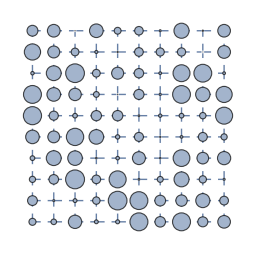

mass before = 44.7051

```mathematica
i=10;grid = GridGraph[{i, i}];   (* generating the input grid graph *)
masses =(#1 -> RandomReal[0.9] & ) /@ VertexList[grid]; (* generates initial masses *)
gridgraph = Graph[grid, VertexWeight -> masses,(* VertexLabels -> Automatic,*) VertexSize -> masses,EdgeStyle->Dashed] (* generating the input grid graph *)
masses=Association[masses];
massQueue=First@massQueuefn[masses,gridgraph];
(* an empty list where the updated maximum vertex is stored after calculation *)
updatedMasses=<||>;
Print["mass before = ",  Total[masses]];
```

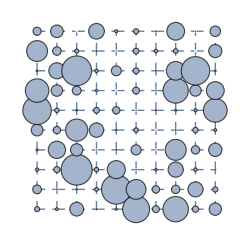

```mathematica
maxIter=100;gridgrapharray={};For[iter=1,iter<=maxIter,iter++,masses=First@MassTransferIteration[masses,gridgraph];gridgraph=makeGrid[masses];AppendTo[gridgrapharray,gridgraph]];gridgraph
```

```mathematica
Manipulate[gridgrapharray[[i]],{i,1,maxIter,1}]
```

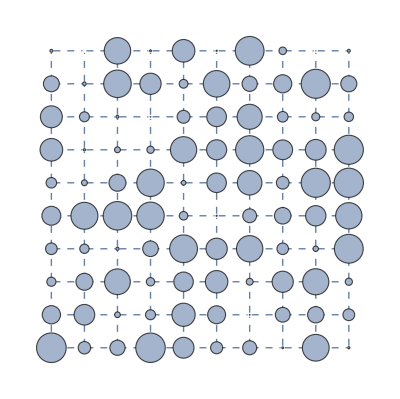
```mathematica
graph0=-Graphics-;
itr1=gridgrapharray[[1]];
itr2=gridgrapharray[[10]];
itr3=gridgrapharray[[50]];
itr4=gridgrapharray[[100]];
GraphicsGrid[{{graph0},{itr1,itr2,itr3,itr4}}]
```

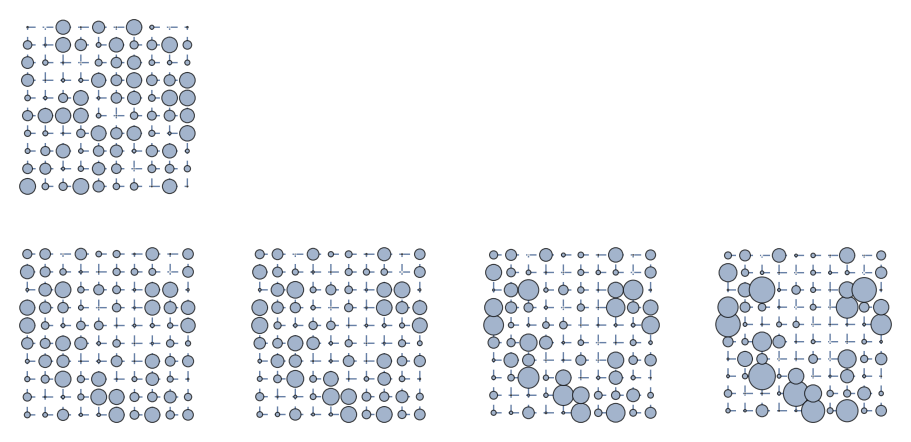

## Future direction

Executing the mass transfer simulation in a grid graph could be the first step towards simulating the aggregation of mass in a random graph. In the Wolfram model framework, the space-time is represented by discrete hypergraph structure. Generating the functions developed in this work to hypergraph model would make this study interesting.
This project could be taken farther by using the package GRAVITAS, which has been developed recently. By utilising this package we can create discrete hypergraph structure of space-time for any metric. Running these functions on FLRW space-time.

## Keywords

LSS

Hypergraph

## Acknowledgment

I would like to express my gratitude to my mentors, Jonathan and Nikola for guiding me setting up the project. I am grateful to them for many interesting discussions and a wonderful learning opportunity to streamline my Mathematica code better. I also thank  Mark Greenberg for helping me debug my code and the wonderful art he made for me. I would also like to thank the entire Summer School team for organizing such an engaging experience. My sincere thanks to Stephen Wolfram for many inspiring talk and meetings. Special thanks to Xerxes, for his time and support, and many interesting discussions over lunch. 
Also I am grateful to Srishti and Debora you guys made my stay at the Bentley University so much fun. 
Finally I can not thank enough my friend Aakash, for inspiring me to apply to the school in the first place, and supporting me throughout.

## References

Some Relativistic and Gravitational Properties of the Wolfram Model- Jonathan Gorard